```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
beta0p36=Flatten[Import["./beta0p36.dat"]];
beta0p37=Flatten[Import["./beta0p37.dat"]];
beta0p38=Flatten[Import["./beta0p38.dat"]];
mub1={0,300,400,500,550,575,600};
```

```mathematica
fitbeta0p36=FindFit[Transpose[{mub1,beta0p36}],a+b x^2+c x^4+d x^6+e x^8,{a,b,c,d,e},x]
fitbeta0p37=FindFit[Transpose[{mub1,beta0p37}],a+b x^2+c x^4+d x^6+e x^8,{a,b,c,d,e},x]
fitbeta0p38=FindFit[Transpose[{mub1,beta0p38}],a+b x^2+c x^4+d x^6+e x^8,{a,b,c,d,e},x]
```

{a→110.775,b→-0.000104719,c→-3.43467×10^-10,d→1.51017×10^-15,e→-2.48979×10^-21}

{a→113.038,b→-0.000105375,c→-3.49841×10^-10,d→1.42805×10^-15,e→-2.32563×10^-21}

{a→115.166,b→-0.000106116,c→-3.35124×10^-10,d→1.23081×10^-15,e→-1.99497×10^-21}

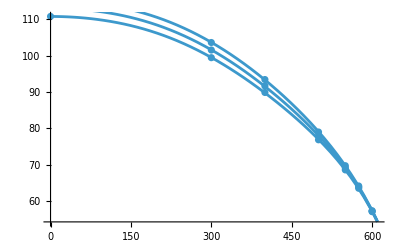

```mathematica
Show[Plot[a+b x^2+c x^4+d x^6+e x^8/.fitbeta0p36,{x,0,610}],ListPlot[Transpose[{mub1,beta0p36}]],Plot[a+b x^2+c x^4+d x^6+e x^8/.fitbeta0p37,{x,0,610}],ListPlot[Transpose[{mub1,beta0p37}]],Plot[a+b x^2+c x^4+d x^6+e x^8/.fitbeta0p38,{x,0,610}],ListPlot[Transpose[{mub1,beta0p38}]]]
```

```mathematica
mub={0,100,200,300,400,500,550,575,600};
beta0p362=Table[{a+b mub[[i]]^2+c mub[[i]]^4+d mub[[i]]^6+e mub[[i]]^8/.fitbeta0p36},{i,1,Length[mub]}];
beta0p372=Table[{a+b mub[[i]]^2+c mub[[i]]^4+d mub[[i]]^6+e mub[[i]]^8/.fitbeta0p37},{i,1,Length[mub]}];
beta0p382=Table[{a+b mub[[i]]^2+c mub[[i]]^4+d mub[[i]]^6+e mub[[i]]^8/.fitbeta0p38},{i,1,Length[mub]}];
Export["beta0p36_fit.dat",beta0p362];
Export["beta0p37_fit.dat",beta0p372];
Export["beta0p38_fit.dat",beta0p382];
```